```mathematica
(*Parameters*)
L=1;
Hp=0.2;
param=10;
Npt=500;
```

```mathematica
(*(*Chebyshev differentiation matrices*)
(*Chebyshev grid and first/second derivative matrices*)
chebPoints=Reverse@Table[Cos[π i/Npt],{i,0,Npt}];
xGrid=L*chebPoints;
(*ListPlot[Transpose[{xGrid,chebPoints}]]*)
T=Table[Cos[π i j/Npt],{i,0,Npt},{j,0,Npt}]; (*DCT matrix*)
c=Join[{2},Table[1,{Npt-1}],{2}];
D1=ConstantArray[0,{Npt+1,Npt+1}];
For[i=1,i<=Npt+1,i++,For[j=1,j<=Npt+1,j++,If[i!=j,D1[[i,j]]=(c[[i]]/c[[j]])*(-1)^(i+j)/(xGrid[[i]]-xGrid[[j]]);,If[i==1,D1[[i,j]]=(2 Npt^2+1)/6;,If[i==Npt+1,D1[[i,j]]=-(2 Npt^2+1)/6;,D1[[i,j]]=0;];];];]];
D1=D1/L;
D2=D1.D1;*)

(*Finite Difference matrices*)
xGrid=Subdivide[-L,L,Npt];  (*Npt+1 points from-L to L*)
dx=xGrid[[2]]-xGrid[[1]];   (*Uniform spacing*)
D1=ConstantArray[0,{Npt+1,Npt+1}];
D2=ConstantArray[0,{Npt+1,Npt+1}];

(*Interior:4th-order centered*)
Do[
D1[[i,i-2]]=1/(12 dx);
D1[[i,i-1]]=-8/(12 dx);
D1[[i,i+1]]=8/(12 dx);
D1[[i,i+2]]=-1/(12 dx);
,
{i,3,Npt-1}
];

(*Left boundary:4th-order forward difference*)
D1[[1]]=Join[{-25,48,-36,16,-3}/(12*dx),ConstantArray[0,Npt+1-5]];
D1[[2]]=Join[{-3,-10,18,-6,1}/(12*dx),ConstantArray[0,Npt+1-5]];
(*Right boundary:4th-order backward difference*)
D1[[Npt]]=Join[ConstantArray[0,Npt+1-5],{-1,6,-18,10,3}/(12*dx)];
D1[[Npt+1]]=Join[ConstantArray[0,Npt+1-5],{3,-16,36,-48,25}/(12*dx)];
(*Interior:4th-order centered*)
Do[D2[[i,i-2]]=-1/(12 *dx^2);
D2[[i,i-1]]=16/(12 *dx^2);
D2[[i,i]]=-30/(12 dx^2);
D2[[i,i+1]]=16/(12 dx^2);
D2[[i,i+2]]=-1/(12 dx^2);,{i,3,Npt-1}];
(*Left boundary rows*)
D2[[1]]=Join[{45,-154,214,-156,61,-10}/(12 dx^2),ConstantArray[0,Npt+1-6]];
D2[[2]]=Join[{11,-20,6,4,-1,0}/(dx^2),ConstantArray[0,Npt+1-6]];
(*Right boundary rows*)
D2[[Npt]]=Join[ConstantArray[0,Npt+1-6],{0,-1,4,6,-20,11}/(dx^2)];
D2[[Npt+1]]=Join[ConstantArray[0,Npt+1-6],{-10,61,-156,214,-154,45}/(12 dx^2)];

(*MatrixPlot[D1,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
MatrixPlot[D2,PlotLabel->"D2: Second Derivative Matrix",ColorFunction->"ThermometerColors",PlotLegends->Automatic]*)
```

```mathematica
(*Define H0(x)*)
H0vals=Hp (1-((xGrid-0.0)/L)^2)+0.001;
(*H0vals=Hp*Exp[-(xGrid/2/(L/4))^2];*)
H0mat = DiagonalMatrix[H0vals];

(*Operator A=D H0 D*)
A=D1.H0mat.D1;

(*Operator B=H0 D^2 H0 (carefully interpreted)*)
B=-param*(H0mat.D2.H0mat);

(*Apply Dirichlet/Neumann BCs at endpoints*)
Aint=A;
Bint=B;
Aint[[1]]=Join[{1},ConstantArray[0,Npt]];
Bint[[1]]=ConstantArray[0,Npt+1];
(*Neumann BC at x =1*)
Aint[[Npt+1]]=D1[[Npt+1]];
Bint[[Npt+1]]=ConstantArray[0,Npt+1];
(*Dirichlet BC at x=1*)
(*Aint[[Npt+1]]=Join[ConstantArray[0,Npt],{1}];
Bint[[Npt+1]]=ConstantArray[0,Npt+1];*)
```

```mathematica
(*Solve eigenvalue problem B v=σ A v*)
{sigmaVals,eigVecs}=Eigensystem[{Bint,Aint},Npt+1];
sigmaVals;
```

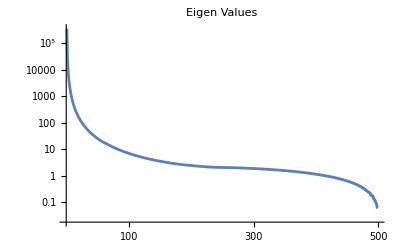

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

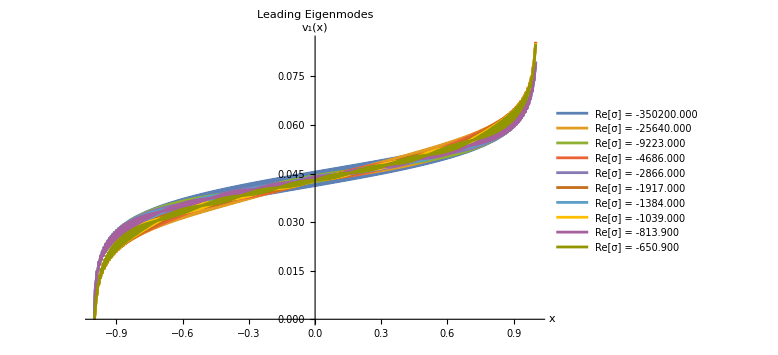

```mathematica
(*Normalize and plot*)
normVecs=Normalize/@eigVecs;
ListLinePlot[Abs[sigmaVals],PlotLabel->"Eigen Values",ScalingFunctions->{"Linear","Log"}]
ListLinePlot[Table[Transpose@{xGrid,Abs[eigVecs[[i]]]},{i,1,10+0*Length[normVecs]}],PlotLabel->"Leading Eigenmodes",PlotLegends->Placed[LineLegend[Table[Row[{"Re[σ] = ",NumberForm[Re[sigmaVals[[i]]],{4,3}]}],{i,Length[sigmaVals]}]],Below],AxesLabel->{"x","v₁(x)"},ImageSize->Large,PlotRange->Full]
```

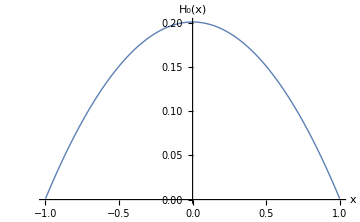
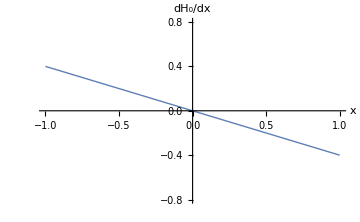

```mathematica
{ListLinePlot[Transpose[{xGrid,H0vals}],AxesLabel->{"x","H₀(x)"},PlotStyle->Thick,PlotRange->Full,ImageSize->Medium],ListLinePlot[Transpose[{xGrid,D1.H0vals}],AxesLabel->{"x","dH₀/dx"},PlotStyle->Thick,PlotRange->{-4*Hp,4*Hp},ImageSize->Medium]}
```

General::munfl: Exp[-3420.29] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

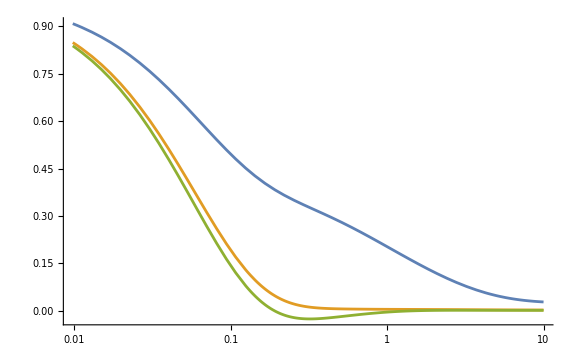

```mathematica
(*Compute v from eigenv vectors and an IC*)
k=Length[sigmaVals];
(*Initial condition for v*)
vIC=ConstantArray[1.0,Npt+1];  (*v(x,0)=1*)
(*vInit=1*Exp[-(xGrid/2/(L/2))^2];*)

Vmat=Transpose[eigVecs[[1;;k]]];  (*modes are columns of eigVecs*)
(*Solve linear problem of coefficients that match IC*)
Subscript[ε, s]=LeastSquares[Vmat,vIC];

v1InterpList=Table[Interpolation[Transpose[{xGrid,Re[Subscript[ε, s][[j]]*eigVecs[[j]]]}]],{j,1,k}];
(*Plot[v1InterpList[[3]][x],{x,-1,1}]*)
v[x_,t_]:=Sum[v1InterpList[[j]][x]*Exp[Re[sigmaVals[[j]]]*t],{j,1,k}];

LogLinearPlot[{v[-0.9,t],v[0,t],v[0.9,t]},{t,0,10},ImageSize->Large,PlotRange->Full]
```